```mathematica
xDot[x_,r_]:=r x+4x^3 - 9x^5
dxDot[x_,r_]=D[xDot[x,r],x]
```

r+12 x^2-45 x^4

```mathematica
sol = Solve[xDot[x,r]==0,x]
X = x/.sol
Xroots[r_] = X
```

{{x→0},{x→-1/3 √(2-√(4+9 r))},{x→1/3 √(2-√(4+9 r))},{x→-1/3 √(2+√(4+9 r))},{x→1/3 √(2+√(4+9 r))}}

{0,-1/3 √(2-√(4+9 r)),1/3 √(2-√(4+9 r)),-1/3 √(2+√(4+9 r)),1/3 √(2+√(4+9 r))}

{0,-1/3 √(2-√(4+9 r)),1/3 √(2-√(4+9 r)),-1/3 √(2+√(4+9 r)),1/3 √(2+√(4+9 r))}

{0,-1/3 √(2-√(4+9 r)),1/3 √(2-√(4+9 r)),-1/3 √(2+√(4+9 r)),1/3 √(2+√(4+9 r))}[1]

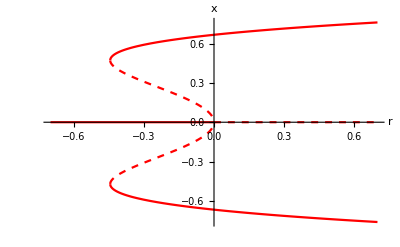

```mathematica
p1 = Plot[{Xroots[r][[2]],Xroots[r][[3]],Xroots[r][[4]],Xroots[r][[5]]},{r,-0.7,0.7},PlotStyle->{{Red, Dashed},{Red, Dashed},{Red},{Red}}];
p2 = Plot[Xroots[r][[1]],{r,-0.7,0},PlotStyle->{Red}];
p3 = Plot[Xroots[r][[1]],{r,0,0.7},PlotStyle->{Red, Dashed}];
g = Show[{p1,p2,p3},AxesLabel->{"r","x"}]
```

```mathematica
Export["/Users/adam/Programming/CAS/DynamicalSystems/Assignment 1/subcritical_pitchfork.png",g,"PNG", ImageSize->1500]
```

/Users/adam/Programming/CAS/DynamicalSystems/Assignment 1/subcritical_pitchfork.png

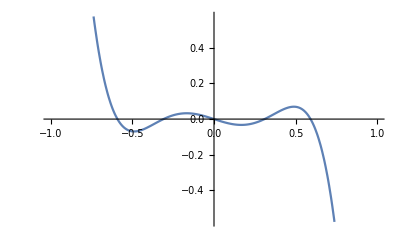

```mathematica
Plot[xDot[x,-0.3], {x,-1,1}]
```

```mathematica
sols= r/.Solve[xDot[x,r]==0,r]
rFix =.;
rFix[x_] = sols
```

{-4 x^2+9 x^4}

{-4 x^2+9 x^4}

```mathematica
Solve[D[rFix[x],x]==0]
```

{{x→0},{x→-(√2)/3},{x→(√2)/3}}

```mathematica
rFix[(√2)/3]
```

{-4/9}